# Video Traking

User interface for video traking by Karolis Misiunas. 
Warning: The routine works slightly differently on Mac and Windowns since M9+ because FFmpeg library is not compatable.

ToDo:
 - [ ] Add multiple ROI processing in UI
 - [ ] Reporting: Running analysis reporting as Monitor[]
 - [ ] FFmpeg: optimise for speed (it is not a bottle neck, but would be nice to have additional ~15%
 - [ ] Processing: run on multiple cores - will speed it up a lot!
 - [ ] Localised intensity correction for treshhold
 - [ ] FFImport frame count is not working properly or relies on Import[]
 - find out what happens when there is poor particle and a good one in intire analysis - might be we include them as singles?!

```mathematica
Quit[];
```

```mathematica
<<VideoAnalysis`
$HistoryLength = 2; (*prevent memory overload*)
SetOptions[FFmpeg, 
  "Colors"->1 (*number of color channels*),
  "ColorCommand"->"gray" (*indicator for "-pix_fmt" parameter:gray/rgb24*)
];
SetOptions[VideoIO,
  "FrameIdFromFrame"-> True,
  "Import" -> FFImport
];
```

## Under the hood functions

```mathematica
FindIntervals[raw_]:= Module[{list},
  list = Sort[ DeleteDuplicates[raw]];
  If[ Length[list] == 0, Return[{}]]; 
  Append[ 
  Reap[FoldList[
    If[#2-Last[#1]==1,
      Append[#1,#2],
      If[Length[#1]==1, Sow[First[#1]], Sow[Interval[{First[#1],Last[#1]}]]];
      {#2}] & ,
    {First[raw]},
    Rest[list]]][[-1,1]],Last[list] 
  ] 
];

processVideo[file_] := Module[{loadTime, analysisTime,oldROI,outputFolder, problems},
  Clear[output];
  oldROI = ROICurrent[] ; (*reuse ROI*)
  Print@Style["===================== " ~~ FileNameTake[file] ~~" =====================", Orange];

  (* === Analyse === *)
  VideoSelect[ file ];
  ROISelect[ oldROI ];
  loadTime = First@AbsoluteTiming[ VideoBufferAll[] ];
  BackgroungUpdate[];
  {analysisTime,output} = AbsoluteTiming @ VideoAnalyse[];

  (* === Report === *)
  problems = VideoProblemInFrames[]⟦;;,1⟧;
  Print[ "Analysis took (load + recognition): "<> ToString@loadTime <> " + "<> ToString@analysisTime<>" = "<> ToString@(loadTime+analysisTime)<>" sec"];
  Print["Particles found: " ,Style[Length[output], Green], ", and problems were in ", Style[Length[problems], Red] , " frames"];
  (*show detection frequancy*)
  Print @ NumberLinePlot[
    { (*FindIntervals[output⟦All, 1⟧],*) FindIntervals[problems]},
    ImageSize->Full
  ];
  (* show background and a selection of bad frames *)
  Print @ Grid[ Partition[
    {Column[{"Background", BackgroundCurrent[]}]}   ~Join~
   If[Length[problems]>1,(Column[{Style[#, Red], VideoGet[#]}] &/@ Sort@RandomChoice[problems,14] ), {}]
  , 5]];
  

  (* === Post Process === *)

  (* mark frames with problems as LQPos *)
  (output⟦#,5⟧ = 0)&/@Position[output⟦;;,1⟧ , _Integer?(MemberQ [problems, #]&)]; 
  (*update time and positions to absolute ones*)
  cornerPos = ROICurrent[]⟦1⟧;
  output⟦All,1⟧ = VideoFrameID /@ output⟦All,1⟧ ; (*time*)
  output⟦All,2⟧ = Round[ output⟦All,2⟧+ cornerPos⟦1⟧ , 0.01]; (*x*)
  output⟦All,3⟧ = Round[ output⟦All,3⟧+ cornerPos⟦2⟧, 0.01]; (*y*)
  (* save to file *)
  outputFolder = FileNameJoin[{DirectoryName[file],"raw_points"}];
  If[ !FileExistsQ[outputFolder] , CreateDirectory[outputFolder ]];

  Print["Done: "<>
  ToString@Export[ FileNameJoin[{outputFolder, (FileBaseName[file] <>".csv")}],  output]];
]
```

## Step 1 - Select sample video file

```mathematica
VideoSelect["F:\\2015-11-24\\1\\200fps_s1.avi"]
```

VideoAddProcessRawFrame: new function count is 1

200fps_s1.avi has 9998 frames and is 200x700

## Step 2 - Select region of intrest

```mathematica
ROISelect[]
```

{{57,670},{163,690}}

```mathematica
ROISelect[{{57,670},{163,690}}]
```

{{57,670},{163,690}}

## Step 3 - Configure tracing algorithm

```mathematica
Options[VideoTracking];

(* Light Particles *)
SetOptions[VideoTracking, 
 "FilterElongation" -> {0.0, 0.5},
 "FilterArea" -> {8,25},
 "UpdateBackgroung" -> False,
 Threshold -> 0.07,
"ForegroundMethod"->"Bright" 
];
```

```mathematica
(* Dark Particles *)
SetOptions[VideoTracking, 
 "FilterElongation" -> {0.0, 0.4},
 "FilterArea" -> {15,38},
 "UpdateBackgroung" -> False,
 Threshold -> 0.2,
"ForegroundMethod"->"Dark" 
];
```

## Step 4 - Test configuration

```mathematica
VideoBufferAll[]
```

Buffer: loaded entire video

```mathematica
VideoFindThreshold[]
```

```mathematica
BackgroungUpdate[]
```

-Graphics-

```mathematica
VideoFrameID[VideoLength[]]
```

2218519

```mathematica
Manipulate[ 
ImageAdjust[ImageSubtract[VideoGet[id], BackgroundCurrent[]], {0.5,5}]

, {id, 1, VideoLength[], 1}]
```

#### Analyse Single Frame

```mathematica
3
```

{{100,29.65,10.08,0.,1.,1.46,3.12,0.18}}

-Graphics-

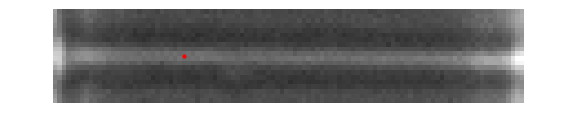

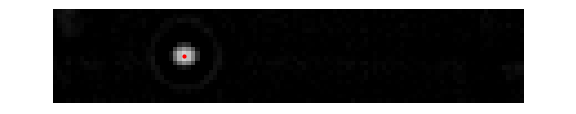

-Graphics-

Area→{1→19.125}

Elongation→{1→0.225261}

FindThreshold→0.28453

```mathematica
frame =0 60 30         +0 30           +100;
(*frame = 3192+2;*)
If[0>=frame||frame >  VideoLength[], frame = 1; Print@"Frame out of range. set to 1."];
ShowTrackOverlayed[img_,list_]:=Show[img,Graphics@Flatten@{Red,Point[#]&/@list[[;;,{2,3}]]},ImageSize->Large]

curPos = VideoAnalyseFrame[frame]
ShowTrackOverlayed[ VideoGet[frame] , curPos]
ShowTrackOverlayed[ BackgroundCurrent[], curPos]
ShowTrackOverlayed[ VideoGetForeground@VideoGet[frame] , curPos] 
ShowTrackOverlayed[ VideoFrameBinarize@VideoGetForeground@VideoGet[frame] , curPos]

"Area"-> ComponentMeasurements[ VideoFrameBinarize@VideoGetForeground@VideoGet[frame] ,"Area"]

"Elongation"-> ComponentMeasurements[ VideoFrameBinarize@VideoGetForeground@VideoGet[frame] ,"Elongation"]
"FindThreshold"-> FindThreshold@VideoGetForeground@VideoGet[frame]
```

## Step 5 - Select file range and run analysis

```mathematica
analyseTheseFiles = FileNames["low_conc_square_wave_(starts_+1V_on_right)2_*.avi","E:\\Experiments\\Antony\\2015-02-12\\",1][[1]]
```

```mathematica
analyseTheseFiles=Select[
(StringReplace[VideoFile[], RegularExpression["\\d+.avi"]-> ""]~~ToString@#~~".avi")&/@ Range[19,100]
,
FileExistsQ];
```

#### Run the analysis

```mathematica
Monitor[
Do[ processVideo[analyseTheseFiles⟦i⟧], {i, Length[analyseTheseFiles] }],
Row[{"Analysing files: ",ProgressIndicator[i,{1,Length[analyseTheseFiles]}],i}," "]
]

Export[
 FileNameJoin[{ DirectoryName@First[analyseTheseFiles], "raw_points", "video_tracking_paramters.txt"}]     ,
ToString@{
"ROI" -> ToString@ROICurrent[],
"VideoTracking" ->Options[VideoTracking]
}
]

Export[
 FileNameJoin[{ DirectoryName@First[analyseTheseFiles], "raw_points", "sample_frame.png"}]     ,
FFImport[VideoFile[], {"Frames", 1}]
];
```

===================== 200fps_s19.avi =====================

VideoAddProcessRawFrame: new function count is 1